## Calculation of the Greens function and the dynamic adjoint in two-group theory

Calculation of the roots of the characteristic equation and criticality

```mathematica
Input data: The four reactors from the Dykin,Jonsson and Pázsit article in Progress 2014, the Behringer-Kosály-Pázsit 1979 NSE article (BWR) and some data from Zsolti (not used yet).
```

MOX

```mathematica
Subscript[D, 1]=1.4719;     (* MOX *)
Subscript[D, 2]= 0.5364;
Subscript[νΣ, f1]= 0.0189;
Subscript[νΣ, f2]= 0.2839;
Subscript[Σ, a1]= 0.0168;
Subscript[Σ, a2]= 0.2818;
Subscript[Σ, R]= 0.0083;
Subscript[Σ, 1]=Subscript[Σ, a1]+Subscript[Σ, R];
Subscript[Σ, 2]=Subscript[Σ, a2];
```

PWR

```mathematica
Subscript[D, 1]=1.4375;     (* PWR *)
Subscript[D, 2]= 0.3723;
Subscript[νΣ, f1]= 0.0056;
Subscript[νΣ, f2]= 0.1405;
Subscript[Σ, a1]= 0.0112;
Subscript[Σ, a2]= 0.1022;
Subscript[Σ, R]= 0.0151;
Subscript[Σ, 1]=Subscript[Σ, a1]+Subscript[Σ, R];
Subscript[Σ, 2]=Subscript[Σ, a2];
```

BWR

```mathematica
Subscript[D, 1]=1.7986;     (* BWR *)
Subscript[D, 2]= 0.4342;
Subscript[νΣ, f1]= 0.0039;
Subscript[νΣ, f2]= 0.0740;
Subscript[Σ, a1]= 0.0074;
Subscript[Σ, a2]= 0.0581;
Subscript[Σ, R]= 0.0131;
Subscript[Σ, 1]=Subscript[Σ, a1]+Subscript[Σ, R];
Subscript[Σ, 2]=Subscript[Σ, a2];
```

CANDU

```mathematica
Subscript[D, 1]=1.4068;     (* CANDU *)
Subscript[D, 2]= 0.8696;
Subscript[νΣ, f1]= 0.0007;
Subscript[νΣ, f2]= 0.0084;
Subscript[Σ, a1]= 0.0011;
Subscript[Σ, a2]= 0.0057;
Subscript[Σ, R]= 0.0100;
Subscript[Σ, 1]=Subscript[Σ, a1]+Subscript[Σ, R];
Subscript[Σ, 2]=Subscript[Σ, a2];
```

```mathematica
BKP 1979
```

```mathematica
Subscript[D, 1]=1.709;     (* BKP *)
Subscript[D, 2]= 0.5290;
Subscript[νΣ, f1]= 0.004653;   (*   x 1.11 for the small system *)
Subscript[νΣ, f2]= 0.07254;      (*   x 1.11 for the small system *)
Subscript[Σ, a1]= 0.07254;
Subscript[Σ, a2]= 0.05940;
Subscript[Σ, R]=0.01271;
Subscript[Σ, 1]=0.02004;
Subscript[Σ, 2]=Subscript[Σ, a2];
β=0.007;
λ=0.1;
Subscript[v, 1]=1.7549*^7;
Subscript[v, 2]=3.9040*^5;
```

Zsolti

```mathematica
Subscript[D, 1]=0.981797;     (* Zsolti *)
Subscript[D, 2]= 0.441232;
Subscript[νΣ, f1]= 0.00489395;
Subscript[νΣ, f2]= 0.0947342;
Subscript[Σ, a1]= 0.00715866;
Subscript[Σ, a2]= 0.0571939;
Subscript[Σ, R]=0.01271;
Subscript[Σ, 1]=0.02004;
Subscript[Σ, 2]=Subscript[Σ, a2];
```

Calculation of the k_eff and the critical size:

```mathematica
Subscript[k, ∞]=(Subscript[νΣ, f1] Subscript[Σ, 2]+Subscript[νΣ, f2] Subscript[Σ, R])/(Subscript[Σ, 1] Subscript[Σ, 2]); Subscript[L2, 1]=Subscript[D, 1]/Subscript[Σ, 1];   Subscript[L2, 2]=Subscript[D, 2]/Subscript[Σ, 2];  (* The diffusion lengts are not used in the dynamic calculations *)
B2=-1/2(1/Subscript[L2, 1]+1/Subscript[L2, 2]-Subscript[νΣ, f1]/Subscript[D, 1])+1/2 √((1/Subscript[L2, 1]+1/Subscript[L2, 2]-Subscript[νΣ, f1]/Subscript[D, 1])^2+4(Subscript[k, ∞]-1)/(Subscript[L2, 1] Subscript[L2, 2]));
Nu2=1/2(1/Subscript[L2, 1]+1/Subscript[L2, 2]-Subscript[νΣ, f1]/Subscript[D, 1])+1/2 √((1/Subscript[L2, 1]+1/Subscript[L2, 2]-Subscript[νΣ, f1]/Subscript[D, 1])^2+4(Subscript[k, ∞]-1)/(Subscript[L2, 1] Subscript[L2, 2]));
B = √B2; H = π/B; a=H/2; Nu = √Nu2;
Print["B = ",B,"    Nu = ",Nu];
Print["k_∞=", Subscript[k, ∞], "        L_1^2 = ",Subscript[L2, 1]," [cm]"," L_2^2 = ",Subscript[L2, 2]," [cm]"];
Print["H = ",H, " [cm]"]
```

B = 0.00853655    Nu = 0.348373

k_∞=1.00672        L_1^2 = 85.2794 [cm] L_2^2 = 8.90572 [cm]

H = 368.017 [cm]

```mathematica
Calculation of the μ(ω) and ν(ω)
Here, we have re-defined Subscript[Σ, 1] such that it also contains the -Subscript[νΣ, f1] term, as in the Victor and Anders article
Subscript[Σ, 1]=Subscript[Σ, a1]+Subscript[Σ, R]-Subscript[νΣ, f1]
```

```mathematica
Sig1[ω_]:=Subscript[Σ, 1]+(ⅈ ω)/Subscript[v, 1]-Subscript[νΣ, f1](1-(ⅈ ω β)/(ⅈ ω+λ));    (* Subscript[Σ, a1]+Subscript[Σ, R] +(ⅈ ω)/Subscript[v, 1]-Subscript[νΣ, f1](1-(ⅈ ω β)/(ⅈ ω+λ)) *)
Sig2[ω_]:=Subscript[Σ, a2]+(ⅈ ω)/Subscript[v, 2];
Nusf1[ω_]=Subscript[νΣ, f1](1-(ⅈ ω β)/(ⅈ ω+λ));
Nusf2[ω_]=Subscript[νΣ, f2](1-(ⅈ ω β)/(ⅈ ω+λ));
```

```mathematica
μ[ω_]:=√(-1/2(Sig1[ω]/Subscript[D, 1]+Sig2[ω]/Subscript[D, 2])+1/2 √((Sig1[ω]/Subscript[D, 1]+Sig2[ω]/Subscript[D, 2])^2-4(Sig1[ω]*Sig2[ω]-Subscript[Σ, R]*Nusf2[ω])/(Subscript[D, 1] Subscript[D, 2])));
ν[ω_]:=√(1/2(Sig1[ω]/Subscript[D, 1]+Sig2[ω]/Subscript[D, 2])+1/2 √((Sig1[ω]/Subscript[D, 1]+Sig2[ω]/Subscript[D, 2])^2-4(Sig1[ω]*Sig2[ω]-Subscript[Σ, R]*Nusf2[ω])/(Subscript[D, 1] Subscript[D, 2])));
```

Calculation of the Greens function.

Define the basic solutions g_μ and g_⋁ as piecewise functions.

```mathematica
Subscript[g, μ][x_,x0_,ω_]:= Piecewise[{{Sin[μ[ω](a+x)]Sin[μ[ω](a-x0)],x<x0},
{Sin[μ[ω](a-x)]Sin[μ[ω](a+x0)],x0<=x}}];
Subscript[g, ν][x_,x0_,ω_]:= Piecewise[{{Sinh[ν[ω](a+x)]Sinh[ν[ω](a-x0)],x<x0},
{Sinh[ν[ω](a-x)]Sinh[ν[ω](a+x0)],x0<=x}}];
```

Define c_μ and c_ν

```mathematica
Subscript[c, μ][ω_]:=(Sig1[ω]+Subscript[D, 1] μ[ω]^2)/Nusf2[ω];  Subscript[c, ν][ω_]:=(Sig1[ω]-Subscript[D, 1] ν[ω]^2)/Nusf2[ω]
```

Define the coefficiens A_μ1..... A_ν2 .

```mathematica
Subscript[A, μ1][ω_]:=(Subscript[c, ν][ω] Nusf2[ω])/((Subscript[D, 1])^2 μ[ω]Sin[2 μ[ω] a](μ[ω]^2+ν[ω]^2));
Subscript[A, ν1][ω_]:=-(Subscript[c, μ][ω]Nusf2[ω])/((Subscript[D, 1])^2 ν[ω]Sinh[2 ν[ω] a](μ[ω]^2+ν[ω]^2));
Subscript[A, μ2][ω_]:=-Nusf2[ω]/(Subscript[D, 1] Subscript[D, 2] μ[ω]Sin[2 μ[ω] a](μ[ω]^2+ν[ω]^2));
Subscript[A, ν2][ω_]:=Nusf2[ω]/(Subscript[D, 1] Subscript[D, 2] ν[ω]Sinh[2 ν[ω] a](μ[ω]^2+ν[ω]^2));
```

Define the Green matrix elements G_11, G_12, G_21 and G_22

```mathematica
Subscript[G, 11][x_,x0_,ω_]:=Subscript[A, μ1][ω]Subscript[g, μ][x,x0,ω]+Subscript[A, ν1][ω]Subscript[g, ν][x,x0,ω];
Subscript[G, 21][x_,x0_,ω_]:=Subscript[c, μ][ω]Subscript[A, μ1][ω]Subscript[g, μ][x,x0,ω]+Subscript[c, ν][ω]Subscript[A, ν1][ω]Subscript[g, ν][x,x0,ω];
Subscript[G, 12][x_,x0_,ω_]:=Subscript[A, μ2][ω]Subscript[g, μ][x,x0,ω]+Subscript[A, ν2][ω]Subscript[g, ν][x,x0,ω];
Subscript[G, 22][x_,x0_,ω_]:=Subscript[c, μ][ω]Subscript[A, μ2][ω]Subscript[g, μ][x,x0,ω]+Subscript[c, ν][ω]Subscript[A, ν2][ω]Subscript[g, ν][x,x0,ω];
```

Plot the space dependence of the absolute value of the four elements of the Green’s matrix with the BWR data of the B-K-P article, as functions of the x variable, for a central perturbation (x_0=0) and ω = 10 rad/s

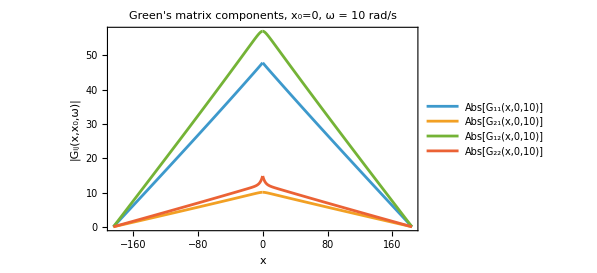

```mathematica
x0 = 0; ω =10;Plot[{Abs[Subscript[G, 11][x,x0,ω]],Abs[Subscript[G, 21][x,x0,ω]],Abs[Subscript[G, 12][x,x0,ω]],Abs[Subscript[G, 22][x,x0,ω]]},{x,-a,a},PlotRange -> Automatic,Frame->True,FrameLabel->{"x","|G_ij(x,x_0,ω)|"},PlotLegends->"Expressions",BaseStyle->{FontFamily->"Helvetica",FontSize->14},PlotLabel->"Green's matrix components, x_0=0, ω = 10 rad/s"]
```

Plot the space dependence of the absolute value of the “removal Green’s function” G_21-G_22, which yields the noise in the thermal group, induced by the fluctuations of the removal cross section Σ_R: (the same as ψ_1^† - ψ_2^† in the B-K-P article):

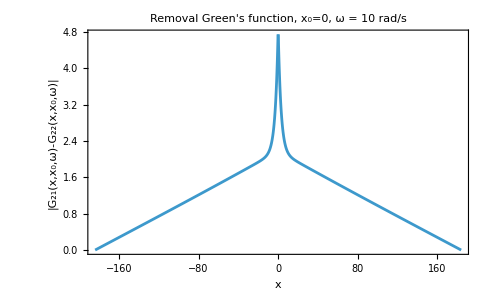

```mathematica
x0=0;ω=10;Plot[Abs[Subscript[G, 21][x,x0,ω]-Subscript[G, 22][x,x0,ω]],{x,-a,a},PlotRange -> Automatic,Frame->True,FrameLabel->{"x","|G_21(x,x_0,ω)-G_22(x,x_0,ω)|"},PlotLegends->"Expressions",BaseStyle->{FontFamily->"Helvetica",FontSize->14},PlotLabel->"Removal Green's function, x_0=0, ω = 10 rad/s"]
```

Plot the freqency dependence of the absolute value of the four elements of the Green’s matrix with the BWR data of the B-K-P article, for x =x_0=0

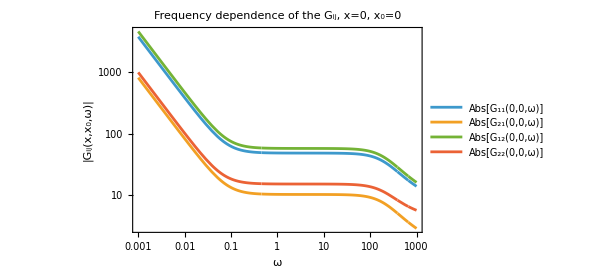

```mathematica
x=0; x0 =0;
LogLogPlot[{Abs[Subscript[G, 11][x,x0,ω]],Abs[Subscript[G, 21][x,x0,ω]],Abs[Subscript[G, 12][x,x0,ω]],Abs[Subscript[G, 22][x,x0,ω]]},{ω,1*^-3,1*^3},PlotRange -> Automatic,Frame->True,Ticks->{Automatic,Table[{10^i,Superscript[10,i]},{i,0,4}]},FrameLabel->{"ω","|G_ij(x,x_0,ω)|"},PlotLegends->"Expressions",BaseStyle->{FontFamily->"Helvetica",FontSize->14},PlotLabel->"Frequency dependence of the G_ij, x=0, x_0=0"]
```

End of material which is of interest to you, the rest is for my own purposes

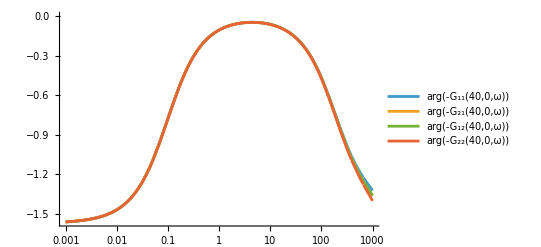

```mathematica
x=40;LogLinearPlot[{Arg[-Subscript[G, 11][x,x0,ω]],Arg[-Subscript[G, 21][x,x0,ω]],Arg[-Subscript[G, 12][x,x0,ω]],Arg[-Subscript[G, 22][x,x0,ω]]},{ω,1*^-3,1*^3},PlotLegends->"Expressions"]
```

Calculation of the adjoint matrix elements.
We need only to define c_μ^†,  c_ν^†, A_μ1^† etc.

```mathematica
SuperDagger[Subscript[c, μ]][ω_]:=(Sig1[ω]+Subscript[D, 1] μ[ω]^2)/Subscript[Σ, R];  SuperDagger[Subscript[c, ν]][ω_]:=(Sig1[ω]-Subscript[D, 1] ν[ω]^2)/Subscript[Σ, R];
```

```mathematica
SuperDagger[Subscript[A, μ1]][ω_]:=(SuperDagger[Subscript[c, ν]][ω] Subscript[Σ, R])/((Subscript[D, 1])^2 μ[ω]Sin[2 μ[ω] a](μ[ω]^2+ν[ω]^2));
SuperDagger[Subscript[A, ν1]][ω_]:=-(SuperDagger[Subscript[c, μ]][ω] Subscript[Σ, R])/((Subscript[D, 1])^2 ν[ω]Sinh[2 ν[ω] a](μ[ω]^2+ν[ω]^2));
SuperDagger[Subscript[A, μ2]][ω_]:=-Subscript[Σ, R]/(Subscript[D, 1] Subscript[D, 2] μ[ω]Sin[2 μ[ω] a](μ[ω]^2+ν[ω]^2));
SuperDagger[Subscript[A, ν2]][ω_]:=Subscript[Σ, R]/(Subscript[D, 1] Subscript[D, 2] ν[ω]Sinh[2 ν[ω] a](μ[ω]^2+ν[ω]^2));
```

```mathematica
SuperDagger[Subscript[G, 11]][x_,x0_,ω_]:=SuperDagger[Subscript[A, μ1]][ω]Subscript[g, μ][x,x0,ω]+SuperDagger[Subscript[A, ν1]][ω]Subscript[g, ν][x,x0,ω];
SuperDagger[Subscript[G, 21]][x_,x0_,ω_]:=SuperDagger[Subscript[c, μ]][ω]SuperDagger[Subscript[A, μ1]][ω]Subscript[g, μ][x,x0,ω]+SuperDagger[Subscript[c, ν]][ω]SuperDagger[Subscript[A, ν1]][ω]Subscript[g, ν][x,x0,ω];
SuperDagger[Subscript[G, 12]][x_,x0_,ω_]:=SuperDagger[Subscript[A, μ2]][ω]Subscript[g, μ][x,x0,ω]+SuperDagger[Subscript[A, ν2]][ω]Subscript[g, ν][x,x0,ω];
SuperDagger[Subscript[G, 22]][x_,x0_,ω_]:=SuperDagger[Subscript[c, μ]][ω]SuperDagger[Subscript[A, μ2]][ω]Subscript[g, μ][x,x0,ω]+SuperDagger[Subscript[c, ν]][ω]SuperDagger[Subscript[A, ν2]][ω]Subscript[g, ν][x,x0,ω];
```

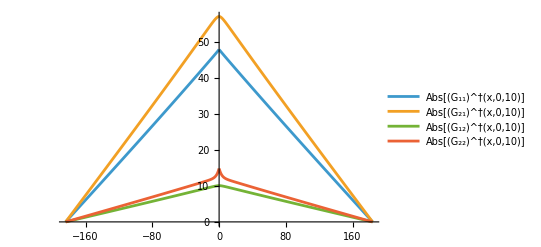

```mathematica
x0 = 0;ω =10;Plot[{Abs[SuperDagger[Subscript[G, 11]][x,x0,ω]],Abs[SuperDagger[Subscript[G, 21]][x,x0,ω]],Abs[SuperDagger[Subscript[G, 12]][x,x0,ω]],Abs[SuperDagger[Subscript[G, 22]][x,x0,ω]]},{x,-a,a},PlotLegends->"Expressions"]
```

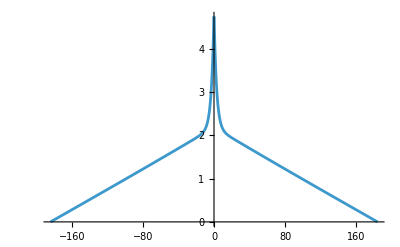

```mathematica
x0=0;ω=1;
Plot[{Abs[SuperDagger[Subscript[G, 12]][x,x0,ω]-SuperDagger[Subscript[G, 22]][x,x0,ω]]},{x,-a,a},PlotLegends->"Expressions"]
```

```mathematica
LogLogPlot[{Abs[SuperDagger[Subscript[G, 11]][x,x0,ω]],Abs[SuperDagger[Subscript[G, 21]][x,x0,ω]],Abs[SuperDagger[Subscript[G, 12]][x,x0,ω]],Abs[SuperDagger[Subscript[G, 22]][x,x0,ω]]},{ω,1*^-3,1*^3},PlotLegends->"Expressions"]
```

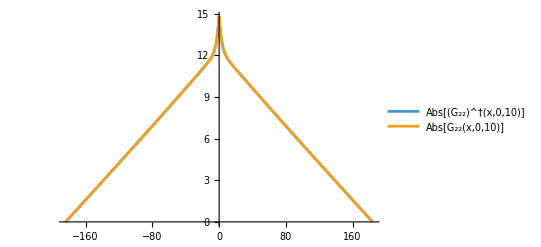

```mathematica
Plot[{Abs[SuperDagger[Subscript[G, 22]][x,x0,ω]],Abs[Subscript[G, 22][x,x0,ω]]},{x,-a,a},PlotLegends->"Expressions"]
```

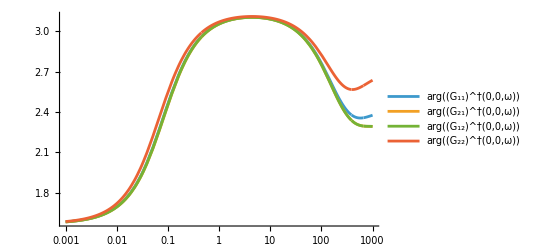

```mathematica
x=0;LogLinearPlot[{Arg[SuperDagger[Subscript[G, 11]][x,x0,ω]],Arg[SuperDagger[Subscript[G, 21]][x,x0,ω]],Arg[SuperDagger[Subscript[G, 12]][x,x0,ω]],Arg[SuperDagger[Subscript[G, 22]][x,x0,ω]]},{ω,1*^-3,1*^3},PlotLegends->"Expressions"]
```

One-group theory with G_0(ω)

```mathematica
Λ=1/(Subscript[v, 2]*Subscript[νΣ, f2]);  β/Λ;
```

198.237

```mathematica
lambda=0.1;beta = 0.007; Lambda = beta/100;
```

```mathematica
ClearAll[G0]
```

```mathematica
G0[ω_]:=1/(ⅈ ω(Lambda+beta/(ⅈ ω + lambda)))
```

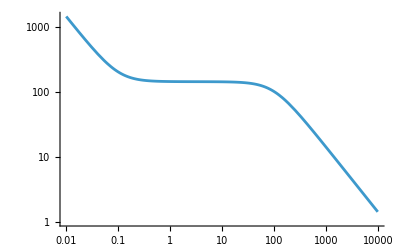

```mathematica
LogLogPlot[Abs[G0[ω]],{ω,1*^-2,1*^4}]
```

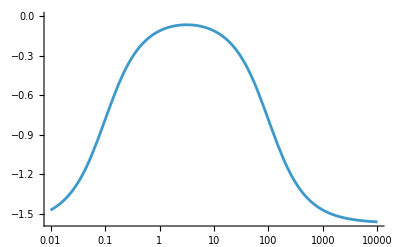

```mathematica
LogLinearPlot[Arg[G0[ω]],{ω,1*^-2,1*^4}]
```